```mathematica
$Path=Union[{NotebookDirectory[],$Path}];
Get@"SVG`"
```

```mathematica
?SVG`*
```

SVG`ExportSVG

ExportSVG[SVG`Private`gr:Blank[Graphics]]:=SVG`Private`distributeDirectives[First[SVG`Private`gr]]

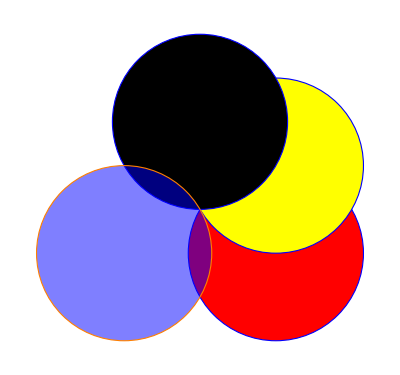

```mathematica
gr=Graphics[{EdgeForm[Directive[Dashed,Blue,Thick]],{Red,Disk[#],{Yellow,Disk[#+{0,1}]}},Disk[#2],{Blue,EdgeForm@Orange,FaceForm@Opacity@.5,Disk[#3]}}&@@CirclePoints[3]]
```

```mathematica
data=ExportString[#,"HTMLFragment"]&/@ExportSVG@gr//Column
```

{<circle fill="RGBColor[1, 0, 0]" posSpec="to be done"></circle>}
{<circle fill="RGBColor[1, 1, 0]" posSpec="to be done"></circle>}
{<circle fill="GrayLevel[0]" posSpec="to be done"></circle>}
{<circle fill="RGBColor[0, 0, 1]" posSpec="to be done"></circle>}

```mathematica
Last@Reap@Scan[Sow[#,directiveType@#]&,data[[2]]]
```

```mathematica
directiveType[c_
```

```mathematica
SVG`Private`mergeDirectives[{GrayLevel[0],EdgeForm[Directive[Dashing[{Small,Small}],RGBColor[0, 0, 1],Thickness[Large]]],RGBColor[1, 0, 0],RGBColor[1, 1, 0]}],Disk[{(√3)/2,1/2}]
```

```mathematica
Graphics[{
Red,EdgeForm[{Blue,Thickness@1}],Disk[]
}]
```

```mathematica
ExportString[XMLElement["tag",{},{}],"HTMLFragment"]
```

<tag></tag>

```mathematica
ExportString[XMLElement["input",{},{}],"HTMLFragment"]
StringReplace[
ExportString[XMLElement["test",{},{}],"HTMLFragment"],
"></"~~LetterCharacter..~~">"~~EndOfString->"/>"
]
```

```mathematica
"<input class=\"form-control\"/>"
```

```mathematica
ExportString[XMLElement["test",{},{}],"XHTML"]
```

<?xml version="1.0" encoding="UTF-8"?>\r
<!DOCTYPE html PUBLIC "-//W3C//DTD XHTML 1.1 plus MathML 2.0//EN"\r
        "HTMLFiles/xhtml-math11-f.dtd">\r
\r
<!-- Created with the Wolfram Language for Students - Personal Use Only : www.wolfram.com -->\r
\r
<html xmlns="http://www.w3.org/1999/xhtml">\r
<head>\r
 <title>\r
  Untitled (the Wolfram Language for Students - Personal Use Only : www.wolfram.com)\r
 </title>\r
 <link href="HTMLFiles/m-9b78793d-2a13-4293-b8df-14487e5c0e02.css" rel="stylesheet" type="text/css" />\r
</head>\r
\r
<body>\r
\r
<p class="Output">\r
 <img src="HTMLFiles/m-9b78793d-2a13-4293-b8df-14487e5c0e02_1.gif" alt="m-9b78793d-2a13-4293-b8df-14487e5c0e02_1.gif" width="186" height="16" style="vertical-align:middle" />\r
</p>\r
\r
\r
\r
\r
<div style="font-family:Helvetica; font-size:11px; width:100%; border:1px none #999999; border-top-style:solid; padding-top:2px; margin-top:20px;">\r
 <a href="http://www.wolfram.com/language/" style="color:#000; text-decoration:none;">\r
  <span style="color:#555555">Created with the Wolfram Language</span> \r
 </a>\r
</div>\r
</body>\r
\r
</html>\r

```mathematica
"<test></test>"
```

```mathematica
StringDelete
```

```mathematica
StringReplace[
ExportString[XMLElement["test",{},{}],"HTMLFragment"],
"></"~~LetterCharacter..~~">"~~EndOfString->">"
]
```

<test>